# Notebook 4 : Solving Nonlinear ODE Systems

The aim of this lab notebook is to familiarize users with various properties of nonlinear systems such as bifurcation & oscillation and make them know the techniques of writing Mathematica program to analyze nonlinear ODE systems.

1.   Stability Analysis

If a system is at steady state,  it should stay there, at least until an external perturbation occurs. Depending on systems behavior after perturbation, their steady states are :

(a) stable (the system returns to this state)
(b) unstable (the system leaves this state) , or 
(c) metastable (the system behavior is indifferent)

To investigate whether a steady state of the ODE system is asymptotically stable , we need to linearize the system  and determine the eigenvalues of the Jacobian matrix. If the real parts of all eigenvalues are less than 0, then the system is stable at that steady state. For two-dimensional systems, depending on the sign of the eigenvalues, the steady states can be distingushed as stable (or unstable) node, stable (or unstable) focus, unstable saddle point and unstable center. (For the details of  how to perform stability analysis, please see the accompanied files: Stability.pdf and Phaseplane.doc).

2.   Limit Cycles

Oscillatory behavior is a typical phenomenon in biology. The cause of the oscillation may be different, either  externally imposed or internally implemented. Internally caused stable oscillations as a function of time can be found if we have a limit cycle in the phase space.

A limit cycle is an isolated trajectory. All tracjectories in its vicinity are periodic solutions winding (stable limit cycle) or away from (unstable) the limit cycle for t→∞.

For example, the nonlinear system dx/dt=x^2 y- x , dy/dt=p- x^2 y has a steady state at (p,1/p). Choosing p=0.98, this steady state is unstable and the time course and phase plane behaviour are shown as follows:

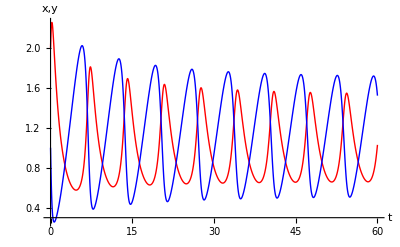

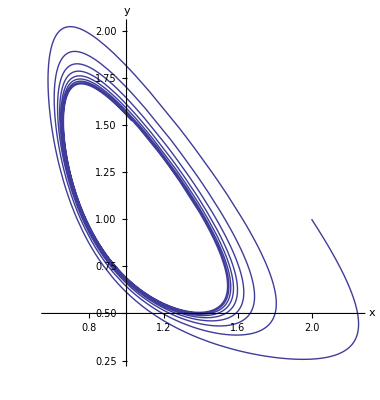

```mathematica
p=0.98;solution=NDSolve[{x'[t]== x[t]^2 y[t]- x[t],y'[t]== p- x[t]^2 y[t],x[0]==2,y[0]==1},{x,y},{t,0,60}];
g1=Plot[Evaluate[{x[t],y[t]}/.solution],{t,0,60},PlotRange->All,PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,1]},AxesLabel->{"t","x,y"}]
g2=ParametricPlot[Evaluate[{x[t],y[t]}/.solution],{t,0,60},PlotRange->All,AxesLabel->{"x","y"}]
```

3.   Bifurcation

Generally we say a bifurcation takes place in a dynamical system if the quality of the behavior of the solutions changes abruptly as some parameter of the system changes. In other words, It is accompanied by a change of the stability of the system. In a bifurcation point, at least one eigenvalue of the Jacobian gets a zero real part. 

For example, considering the Higgins-Sel'kov oscillator :
  dx/dt= a-xy^2
  dy/dt=xy^2-2y
where a>0.The steady state of the system can be easily determined to be (4/a,a/2). The Jacobian matrix can be determined as follows:

```mathematica
jac=Outer[D,{a-x y y,x y y-2 y},{x,y}]/.{x->4/a,y->a/2}//MatrixForm
```

(-a^2/4 | -4
a^2/4 | 2)

The determinant of the system is a^2/2 which means that the determinant is always positive. However the trace of the Jacobian matrix is 2-0.25a^2 changes its sign at a=2√2 which means there is a bifurcation point there. To verify this,  firstly we let a=2.5 and solve the systems for an initial condition of x(0)=2 and y(0)=1:

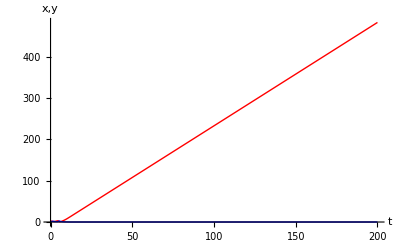

```mathematica
a=2.5;solution=NDSolve[{x'[t]== a-x[t] y[t]^2 ,y'[t]== x[t] y[t]^2-2 y[t],x[0]==2,y[0]==1},{x,y},{t,0,200}];
g1=Plot[Evaluate[{x[t],y[t]}/.solution],{t,0,200},PlotRange->All,PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,1]},AxesLabel->{"t","x,y"}]
```

Obviously for a=2.5, the system is unstable since x increases infinitely. However, if we increases a to 2.9 and solve the systems again:

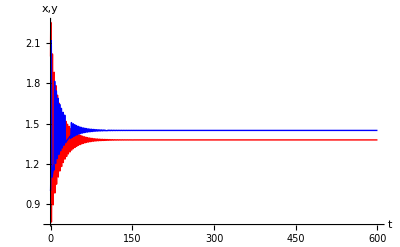

```mathematica
a=2.9;solution=NDSolve[{x'[t]== a-x[t] y[t]^2 ,y'[t]== x[t] y[t]^2-2 y[t],x[0]==2,y[0]==1},{x,y},{t,0,600}];
g1=Plot[Evaluate[{x[t],y[t]}/.solution],{t,0,600},PlotRange->All,PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,1]},AxesLabel->{"t","x,y"}]
```

From the above graph, we can see that now the system goes to its steady state. So when a increases from 2.5 to 2.9, the quality of the behavior of the system changes (from being unstabel to being stable),  and this is just the phenomenon of bifurcation.

4.  Exercises

### Exercise 1: Dynamics of Circulating Blood Cells

Assume that the densities of circulating blood cells (density x) is controlled by a hormonal agent (y) produced by the blood cells. The dynamics are determined by the differential equations :
      dx/dt = (2 y)/(1+y^2)-x,
      dy/dt = x-y.
(i) Determine the steady states for x, y ≥0.
(ii) Sketch the flows in the (x,y)-phase plane for x,y≥0.
(iii) For an initial condition of x(0)=10, y(0)=0.1, what will happen in the limit t→∞?

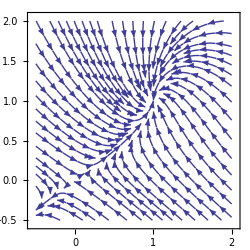

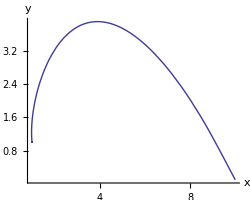

```mathematica
StreamPlot[{2y/(1+y^2)-x,x-y},{x,-0.5,2},{y,-0.5,2},ImageSize->250]
sol = NDSolve[{x'[t]==(2 y[t]/(1 + y[t]^2) - x[t]), y'[t]==(x[t] - y[t]),x[0]==10,y[0]==0.1},{x,y},{t,0,100}];
ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,100},PlotRange->All,AxesLabel->{"x","y"},AxesOrigin->{0,0},ImageSize->250]
```

### Exercise 2: Limpets and Seaweed

Limpets and seaweed live in a tidepool. The dynamics of this system are given by the differential equations
   ds/dt=s-s^2-s l, 
   dl/dt=sl-l/2-l^2,     l≥0,  s≥0,
where the densities of seaweed and limpets are given by s and l, respectively.
(i) Determine all steady states in this sytem.
(ii) For each nonzero steady state determined in part (i), evaluate the stability and classify it as a node, focus, or saddle point.
(iii) Sketch the flows in the phase plane.
(iv) What will the dynamics be in the limit as t→∞ for initial conditions:
 (a)  s(0)=0, l(0)=0?    (b) s(0)=0, l(0)=15?   (c)s(0)=2, l(0)=0?  (d)s(0)=2, l(0)=15?

{{s→0,l→-1/2},{s→0,l→0},{s→3/4,l→1/4},{s→1,l→0}}

{1/4 (-2+ⅈ √2),1/4 (-2-ⅈ √2)}

{-1,1/2}

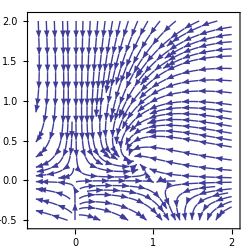

{{0.,0.}}

{{0.,-8.79636×10^-12}}

{{1.,-2.16298×10^-27}}

{{0.75,0.25}}

```mathematica
sol=Solve[{s-s^2 - s l==0,s l - l/2 - l^2==0},{s,l}]
jac1=Eigenvalues[Outer[D,{s-s^2- s l,s l - l/2 -l^2},{s,l}]/.sol[[3]]]
jac1=Eigenvalues[Outer[D,{s-s^2- s l,s l - l/2 -l^2},{s,l}]/.sol[[4]]]

StreamPlot[{s-s^2-s l,s l -l/2-l^2},{s,-0.5,2},{l,-0.5,2},ImageSize->250]

sol1=NDSolve[{s'[t]== s[t] - s[t]^2-s[t] l[t],l'[t]== s[t] l[t] - l[t]/2 -l[t]^2,s[0]==0,l[0]==0},{s,l},{t,0,60}];
Evaluate[{s[t],l[t]}/.sol1]/.t->60
sol1=NDSolve[{s'[t]== s[t] - s[t]^2-s[t] l[t],l'[t]== s[t] l[t] - l[t]/2 -l[t]^2,s[0]==0,l[0]==15},{s,l},{t,0,60}];
Evaluate[{s[t],l[t]}/.sol1]/.t->60
sol1=NDSolve[{s'[t]== s[t] - s[t]^2-s[t] l[t],l'[t]== s[t] l[t] - l[t]/2 -l[t]^2,s[0]==2,l[0]==0},{s,l},{t,0,60}];
Evaluate[{s[t],l[t]}/.sol1]/.t->60
sol1=NDSolve[{s'[t]== s[t] - s[t]^2-s[t] l[t],l'[t]== s[t] l[t] - l[t]/2 -l[t]^2,s[0]==2,l[0]==15},{s,l},{t,0,60}];
Evaluate[{s[t],l[t]}/.sol1]/.t->60
```

### Exercise 3: Brusselator Oscillator

The "Brusselator" is a mathematical model for chemical oscillations. The equations for the Brusselator are 
   du/dt = a- ( b + 1 ) u +  u^2 v,

    dv/dt= b u- u^2 v, 
 where u≥0,  v≥0,  and a , b are positive constants.
 (i) Determine the values of u and v in terms of a and b at the steady state(s).
 (ii) Find the characteristic equation that can be used to determine the stability of the steady state(s) and solve this equation.
 (iii) If u is held constant at some nonzero value (i.e., du/dt=0), what will be the behavior of v starting at different initial conditions ?
 (iv) If we assume a as a fixed parameter, determine the bifurcation point of b as it varies. Make some simulations to verify your conclusion.
 (v) (optional) Make a bifurcation diagram for x as a function of b assuming a=1.

{{u→a,v→b/a}}

a^2+λ+a^2 λ-b λ+λ^2

{{λ→1/2 (-1-a^2-√(-4 a^2+(1+a^2-b)^2)+b)},{λ→1/2 (-1-a^2+√(-4 a^2+(1+a^2-b)^2)+b)}}

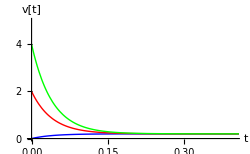

-1-a^2+b

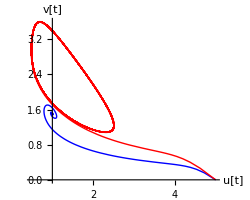

```mathematica
sol = Solve[{a-(b+1)u + u^2 v==0,b u - u^2 v==0},{u,v}]
eq = Det[(Outer[D,{a-(b+1) u + u^2 v,b u - u^2 v},{u,v}]/.Flatten[sol])-λ IdentityMatrix[2]]
Solve[eq==0,λ]

sol1 = Table[NDSolve[{u'[t]==0,v'[t]==(b u[t] -u[t]^2 v[t])/.b->1,v[0]==i,u[0]==5},{u,v},{t,0,100}],{i,0,4,2}];
Show[Plot[Evaluate[{v[t]}/.sol1[[1]]],{t,0,1},PlotRange->{{0,0.4},{0,5}},AxesLabel->{"t","v[t]"},PlotStyle->Blue,ImageSize->250],
Plot[Evaluate[{v[t]}/.sol1[[2]]],{t,0,1},PlotRange->{{0,0.4},{0,5}},AxesLabel->{"t","v[t]"},PlotStyle->Red,ImageSize->250],Plot[Evaluate[{v[t]}/.sol1[[3]]],{t,0,1},PlotRange->{{0,0.4},{0,5}},AxesLabel->{"t","v[t]"},PlotStyle->Green,ImageSize->250]]

Tr[Outer[D,{a-(b+1) u + u^2 v,b u - u^2 v},{u,v}]/.Flatten[sol]]
sol1 = NDSolve[{u'[t]==(a-(b+1)u[t] +u[t]^2 v[t])/.{a->1,b->2.5},v'[t]==(b u[t] -u[t]^2 v[t])/.b->2.5,v[0]==0,u[0]==5},{u,v},{t,0,100}];
sol2 = NDSolve[{u'[t]==(a-(b+1)u[t] +u[t]^2 v[t])/.{a->1,b->1.5},v'[t]==(b u[t] -u[t]^2 v[t])/.b->1.5,v[0]==0,u[0]==5},{u,v},{t,0,100}];
Show[ParametricPlot[Evaluate[{u[t],v[t]}/.sol2],{t,0,100},PlotRange->All,AxesLabel->{"u[t]","v[t]"},PlotStyle->Blue,ImageSize->250],ParametricPlot[Evaluate[{u[t],v[t]}/.sol1],{t,0,100},PlotRange->All,AxesLabel->{"u[t]","v[t]"},PlotStyle->Red,ImageSize->250]]
```

### Exercise 4: Fitzhugh-Nagumo Equations

In an excitable system such as a neuron, a small deviation from a stable steady state can lead to a large excursion before the steady state is reestablished. Fitzhugh-Nagumo equations are a famous model  for neuron. Consider the following differential equations which are a form of classical Fitzhugh-Nagumo equations:
      dx/dt =1/ϵ(y- x^3/12+x),
      dy/dt =-ϵ(2 x+y-8/3),     1≫ϵ>0.
 (i) Determine the steady state of this system, evaluate its stability and classify it as node, focus or saddle point.
 (ii) Assume ϵ=0.1, solve the equations and plot x and y as functions of t  for an initial condition of x(0)=1, y(0)= -4/3 . Plot the orbit of (x,y) together with the flow and nullclines in the x-y phase plane.  Try some other initial conditions and plot the orbits in the phase plane.

{{x→2,y→-4/3},{x→-1-ⅈ √15,y→2/3 (7+3 ⅈ √15)},{x→-1+ⅈ √15,y→2/3 (7-3 ⅈ √15)}}

{1/2 (-ϵ-√(-8+ϵ^2)),1/2 (-ϵ+√(-8+ϵ^2))}

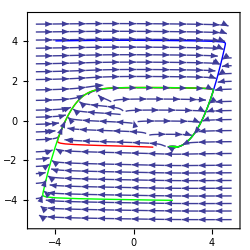

```mathematica
sol=Solve[{1/ϵ(y - x^3/12 + x)==0, -ϵ(2 x + y - 8/3)==0},{x,y}]
jac1=Eigenvalues[Outer[D,{1/ϵ(y - x^3/12 + x), -ϵ(2 x + y - 8/3)},{x,y}]/.sol[[1]]]

sol1 = NDSolve[{x'[t]==(1/ϵ(y[t] - x[t]^3/12 + x[t]))/.ϵ->0.1, y'[t]==(-ϵ(2 x[t] + y[t] - 8/3))/.ϵ->0.1,x[0]==1,y[0]==-4/3},{x,y},{t,0,100}];
sol2 = NDSolve[{x'[t]==(1/ϵ(y[t] - x[t]^3/12 + x[t]))/.ϵ->0.1, y'[t]==(-ϵ(2 x[t] + y[t] - 8/3))/.ϵ->0.1,x[0]==-4,y[0]==4},{x,y},{t,0,100}];
sol3 = NDSolve[{x'[t]==(1/ϵ(y[t] - x[t]^3/12 + x[t]))/.ϵ->0.1, y'[t]==(-ϵ(2 x[t] + y[t] - 8/3))/.ϵ->0.1,x[0]==2,y[0]==-4},{x,y},{t,0,100}];
Show[StreamPlot[{(1/ϵ(y - x^3/12 + x))/.ϵ->0.1,(-ϵ(2 x + y - 8/3))/.ϵ->0.1},{x,-5,5},{y,-5,5}],
ParametricPlot[Evaluate[{x[t],y[t]}/.sol1],{t,0,100},PlotRange->All,AxesLabel->{"x","y"},AxesOrigin->{0,0},PlotStyle->Red],
ParametricPlot[Evaluate[{x[t],y[t]}/.sol2],{t,0,100},PlotRange->All,AxesLabel->{"x","y"},AxesOrigin->{0,0},PlotStyle->Blue],ParametricPlot[Evaluate[{x[t],y[t]}/.sol3],{t,0,100},PlotRange->All,AxesLabel->{"x","y"},AxesOrigin->{0,0},PlotStyle->Green],ImageSize->250]
```

### Exercise 5: Morris-Lecar Model (optional)

Under constant curreent injection barnacle muscle fibers respond with a host of oscillatory voltage waveforms. Morris and Lecar (1981) proposed a simple model  to explain this phenomenon. Their model involves a fast activating Ca^(2+)current, a delayed rectifier K^+ currentand a passive leak. The model translates into two equations :

CdV/dt=-g_Cam_∞(V-V_Ca)-g_Kw(V-V_K)-g_L(V-V_L)+I_app,
dw/dt=(ϕ(w_∞-w))/τ,

where m_∞=0.5[1+tanh((V-v_1)/v_2)],    w_∞=0.5[1+tanh((V-v_3)/v_4)],     τ=1/cosh((V-v_3)/(2*v_4)).   
The parameters are : C=20μF/cm^2,  V_K=-84mV,  g_K=8mS/cm^2, V_Ca=120mV, g_Ca=4.4mS/cm^2, V_L=-60mV, g_L=2mS/cm^2, v_1=-1.2mV,v_2=18mV,v_3=2mV,v_4=30mV and ϕ=0.04/ms.
(i)  Assume I_app=150pA, solve the equations and plot voltage V as function of t (say, t from 0 to 200ms) for an initial condition of x(0)=0, y(0)= 0. Plot the orbit of (V,w) together with the flow and nullclines in the V-w phase plane. (Hint : In current case, you need not be bothered by the units, just use the parameter values directly)
(ii) Now assume  I_app=60pA or 200pA, solve the equations and plot voltage V as function of t  (say, t from 0 to 200ms) for an initial condition of x(0)=0, y(0)= 0 and make comparison with the corresponding curve which you have obtained in (i). Give explanation for the difference if you find any.
(iii) Make a bifurcation diagram for V as a function of   I_app.

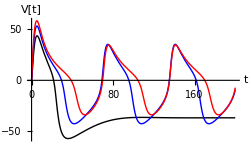

```mathematica
sol = Table[NDSolve[{20*V'[t] ==-4.4*0.5(1 + Tanh[(V[t]+1.2)/18])(V[t]-120)-8*w[t](V[t]+84)-2(V[t]+60) + i,w'[t]==0.04*(0.5(1 + Tanh[(V[t]-2)/30])-w[t])/(1/Cosh[(V[t]-2)/(2*30)]),V[0]==0,w[0]==0},{V,w},{t,0,200}],{i,{60,150,200}}] ;
Plot[{Evaluate[{V[t]}/.sol[[1]]],Evaluate[{V[t]}/.sol[[2]]],Evaluate[{V[t]}/.sol[[3]]]},{t,0,200},PlotRange->All,AxesLabel->{"t","V[t]"},PlotStyle->{Black,Blue,Red},ImageSize->250]

Show[VectorPlot[{-4.4*0.5(1 + Tanh[(V+1.2)/18])(V-120)-8*w(V+84)-2(V+60) + 150,0.04*(0.5(1 + Tanh[(V-2)/30])-w)/(1/Cosh[(V-2)/(2*30)])},{V,-50,50},{w,-1,1}],
ParametricPlot[{Evaluate[{V[t],w[t]}/.sol[[1]]],Evaluate[{V[t],w[t]}/.sol[[2]]],Evaluate[{V[t],w[t]}/.sol[[3]]]},{t,0,200},AxesLabel->{"V","w"},PlotStyle->{Black,Blue,Red}]]
```